```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
mub={0,50,100,150,200,250,300,350,400,450,500,550,575,600,625,650,675,700};
fitdata=Table[Import["./mub"<>ToString[mub[[i]]]<>".dat"],{i,1,Length[mub]}];
```

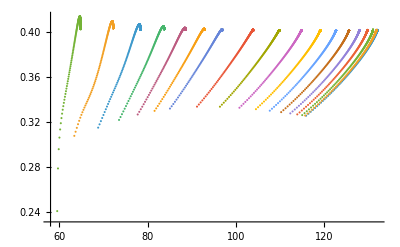

```mathematica
ListPlot[fitdata,PlotRange->All]
```

```mathematica
fitfun=Table[Interpolation[fitdata[[i]]],{i,1,Length[mub]}];
```

```mathematica
Table[Flatten[FindRoot[fitfun[[i]][x]-0.34==0,{x,fitdata[[i]][[-1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
```

{120.14,119.878,119.09,117.768,115.904,113.484,110.493,106.918,102.752,97.9898,92.6251,86.6074,83.3038,79.7443,75.8487,71.493,66.5246,61.1537}

```mathematica
Export["betaregion.dat",%]
```

betaregion.dat

```mathematica
Export["mub.dat",mub]
```

mub.dat